```mathematica
α=(-g^2 l^2)/(p3^2-p0^2); β=(-g^2 k^2)/(p3^2-p0^2);g=0.5;l=1;k=2;p0=3;p3=1;Ag=0.01;wg=5;
```

```mathematica
unϕ[z_,t_]=JacobiCN[p0 t+p3 z,1/2]/(√β)
```

```mathematica
unψ[z_,t_]=JacobiCN[p0 t+p3 z,1/2]/(√α)
```

```mathematica
hpc[z_,t_]=Ag (wg t-I)Exp[-I wg(t-z)]
```

0.01 ⅇ^(-20 ⅈ (t-z)) (-ⅈ+20 t)

```mathematica
eqnc={-D[u[z,t],t,t]+D[u[z,t],z,z]-2 l^2 g^2 unϕ[z,t]unψ[z,t]v[z,t]-g^2 l^2 unψ[z,t]^2 u[z,t]== D[hpc[z,t],t]D[unϕ[z,t],t]- D[hpc[z,t],z]D[unϕ[z,t],z]-hpc[z,t](-D[unϕ[z,t],t,t]+D[unϕ[z,t],z,z]),-D[v[z,t],t,t]+D[v[z,t],z,z]-2 k^2 g^2 unϕ[z,t]unψ[z,t]u[z,t]-g^2 k^2 unϕ[z,t]^2 v[z,t]== -D[hpc[z,t],t]D[unψ[z,t],t]+ D[hpc[z,t],z]D[unψ[z,t],z]+hpc[z,t](-D[unψ[z,t],t,t]+D[unψ[z,t],z,z])};
```

```mathematica
icc={u[z,-15]==  0,v[z,-15]== 0};
```

```mathematica
bcc={Derivative[0,1][u][z,-15]== 0,Derivative[0,1][v][z,-15]==0,u[0,t]== 0,v[0,t]== 0,Derivative[1,0][u][0,t]== 0,Derivative[1,0][v][0,t]==0};
```

```mathematica
dsolc=NDSolve[{eqnc,bcc,icc},{u,v},{t,-15,0},{z,0,5},AccuracyGoal->3,PrecisionGoal->2,Method->{"MethodOfLines",Method->"StiffnessSwitching","SpatialDiscretization"->{"TensorProductGrid","MaxStepSize"->0.05}}]
```

{{u→InterpolatingFunction[{{0., 5.}, {-15., 0.}}, <>],v→InterpolatingFunction[{{0., 5.}, {-15., 0.}}, <>]}}

```mathematica
phic=u/.dsolc[[1]]
```

InterpolatingFunction[{{0., 5.}, {-15., 0.}}, <>]

```mathematica
psic=v/.dsolc[[1]]
```

InterpolatingFunction[{{0., 5.}, {-15., 0.}}, <>]

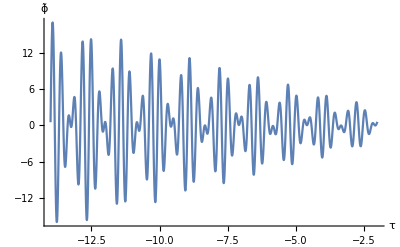

```mathematica
Plot[Re[phic[1,t]],{t,-14,-2},AxesLabel->{τ,ϕ̃}]
```

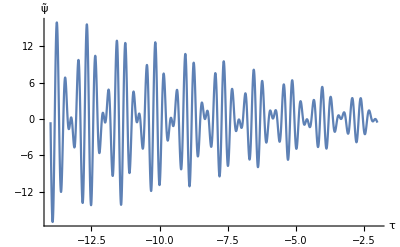

```mathematica
Plot[Re[psic[1,t]],{t,-14,-2},AxesLabel->{τ,ψ̃}]
```

```mathematica
Plot3D[Re[phic[z,t]],{z,0.,4.},{t,-14.,-4},AxesLabel->{z,τ},Filling->Bottom,ColorFunction->Function[{z,t,y},Hue[0.7y]],PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[Re[psic[z,t]],{z,0.,4.},{t,-14.,-4},AxesLabel->{z,τ},Filling->Bottom,ColorFunction->Function[{z,t,y},Hue[0.7y]],PlotRange->Full]
```

-Graphics3D-

Spectrum Analysis

```mathematica
src=100;
datac=Table[Re[phic[1,t]],{t,-14,-2,1/src}];
nnc=Length@datac;
```

```mathematica
ftc=Fourier[datac,FourierParameters->{-1,-1}];
freqsc=Table[f,{f,0,src(nnc-1)/nnc,src/nnc}];
```

```mathematica
ddc=Table[If[i<(nnc-1)/2,Abs[ftc][[i]],0.],{i,1,nnc}];
```

```mathematica
Print[N[freqsc[[Ordering[ddc,{-1}][[1]]]]]",",Abs[ftc][[Ordering[ddc,{-1}][[1]]]]]
```

3.16403 ,0.00457574

```mathematica
xx=Table[If[i<30,ddc[[i]],0.],{i,1,nnc}];
```

```mathematica
xx1=Table[If[i>50,ddc[[i]],0.],{i,1,nnc}];
```

```mathematica
xx2=xx+xx1;
```

```mathematica
N[freqsc[[Ordering[xx1,{-1}][[1]]]]]
```

4.41299

```mathematica
Ordering[xx,{-1}][[1]]
```

25

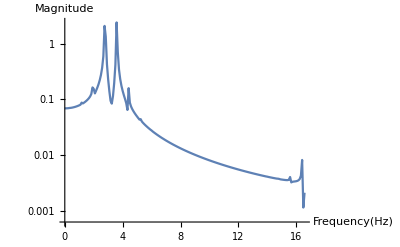

```mathematica
ListLogPlot[Transpose[{freqsc,Abs[ftc]}][[1;;200]],PlotRange->All,Joined->True,AxesLabel->{"Frequency(Hz)","Magnitude"}]
```

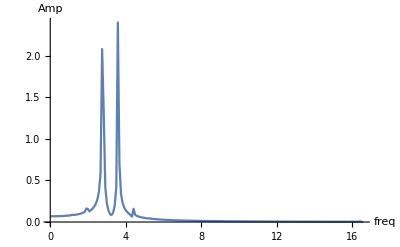

```mathematica
ListLinePlot[Transpose[{freqsc,Abs[ftc]}][[1;;200]],PlotRange->All,Joined->True,AxesLabel->{freq,Amp}]
```

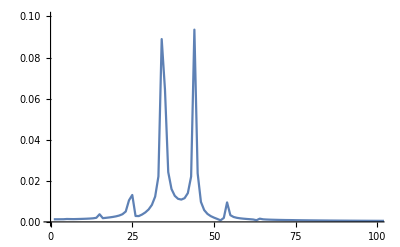

```mathematica
ListLinePlot[Abs[ftc],PlotRange->{{0,100},{0,.1}}]
```

```mathematica
Spectrogram[datac,SampleRate->100,FrameLabel->{"Time(s)","Frequency(Hz)"},PlotLegends->Automatic]
```

-Graphics-